# Chapter 1: Quantum measurement

## Author: Bruno O. Goes

#### 1) Useful functions

```mathematica
(*Setting the path where the plots are going to be saved.*)
nbdirectory=SetDirectory[NotebookDirectory[]];
PlotsPathChap1=nbdirectory<>"/PlotsChap1/";

alphabetlabel={"(a)","(b)","(c)","(d)","(e)","(f)","(g)","(h)","(i)","(j)","(k)","(l)","(m)","(n)","(o)","(p)","(q)","(r)","(s)","(t)","(u)","(v)","(w)","(x)","(y)","(z)"};
```

```mathematica
(*Drawing the Poicaré sphere: based on Melt's code*)
PoincareSphere[labels_:True]:=Module[{splineCircle,pointsAndConnection,surroundingCircles,texKet},splineCircle[m_List,r_,angles_List:{0,2 π}]:=Module[{seg,ϕ,start,end,pts,w,k},{start,end}=Mod[N[angles],2 π];If[end≤start,end+=2 π];seg=Quotient[N[end-start],π/2];ϕ=Mod[N[end-start],π/2];If[seg==4,seg=3;ϕ=π/2];pts=(r RotationMatrix[start].#1&)/@Join[Take[{{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1}},2 seg+1],(RotationMatrix[(seg π)/2].#1&)/@{{1,Tan[ϕ/2]},{Cos[ϕ],Sin[ϕ]}}];If[Length[m]==2,pts=(m+#1&)/@pts,pts=(m+#1&)/@Transpose[Append[Transpose[pts],ConstantArray[0,Length[pts]]]]];w=Join[Take[{1,1/(√2),1,1/(√2),1,1/(√2),1},2 seg+1],{Cos[ϕ/2],1}];k=Join[{0,0,0},(Riffle[#1,#1]&)[Range[seg+1]],{seg+1}];BSplineCurve[pts,SplineDegree->2,SplineKnots->k,SplineWeights->w]]/;Length[m]==2||Length[m]==3;pointsAndConnection[points_]:=(Sequence@@{Sequence@@Point/@#1,Line[#1]}&)[points];surroundingCircles=GeometricTransformation[splineCircle[{0,0,0},1],{{RotationMatrix[0,{1,0,0}],{0,0,0}},{RotationMatrix[π/2,{1,0,0}],{0,0,0}},{RotationMatrix[π/2,{0,1,0}],{0,0,0}}}];texKet[n_]:=Text[Style[StringTemplate["\!\(\*TemplateBox[{\"`1`\"},\n\"Ket\"]\)"][ToString[n]],FontFamily->"Times",20]];Graphics3D[{White,Opacity[0.3],Sphere[{0,0,0},1],Opacity[1],Thickness[0.004],PointSize[0.02],Red,pointsAndConnection[{{0,0,1},{0,0,-1}}],Blue,pointsAndConnection[{{1,0,0},{-1,0,0}}],Darker[Green],pointsAndConnection[{{0,1,0},{0,-1,0}}],Black,Point[{0,0,0}],If[labels==True,{Text[texKet["R"],{0,0,1.2}],Text[texKet["L"],{0,0,-1.2}],Text[texKet["H"],{1.2,0,0}],Text[texKet["V"],{-1.2,0,0}],Text[texKet["A"],{0,1.2,0}],Text[texKet["D"],{0,-1.2,0}]}],Gray,Thin,surroundingCircles},Boxed->False,PlotRange->ConstantArray[{-1.2,1.2},3],ImageSize->500,RotationAction->"Clip"]]
```

```mathematica
PoincareSphere[]
```

-Graphics3D-

```mathematica
(*Drawing the spin Bloch sphere: based on Melt's code*)
BlochSphereSpin[labels_:True]:=Module[{splineCircle,pointsAndConnection,surroundingCircles,texKet},splineCircle[m_List,r_,angles_List:{0,2 π}]:=Module[{seg,ϕ,start,end,pts,w,k},{start,end}=Mod[N[angles],2 π];If[end≤start,end+=2 π];seg=Quotient[N[end-start],π/2];ϕ=Mod[N[end-start],π/2];If[seg==4,seg=3;ϕ=π/2];pts=(r RotationMatrix[start].#1&)/@Join[Take[{{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1}},2 seg+1],(RotationMatrix[(seg π)/2].#1&)/@{{1,Tan[ϕ/2]},{Cos[ϕ],Sin[ϕ]}}];If[Length[m]==2,pts=(m+#1&)/@pts,pts=(m+#1&)/@Transpose[Append[Transpose[pts],ConstantArray[0,Length[pts]]]]];w=Join[Take[{1,1/(√2),1,1/(√2),1,1/(√2),1},2 seg+1],{Cos[ϕ/2],1}];k=Join[{0,0,0},(Riffle[#1,#1]&)[Range[seg+1]],{seg+1}];BSplineCurve[pts,SplineDegree->2,SplineKnots->k,SplineWeights->w]]/;Length[m]==2||Length[m]==3;pointsAndConnection[points_]:=(Sequence@@{Sequence@@Point/@#1,Line[#1]}&)[points];surroundingCircles=GeometricTransformation[splineCircle[{0,0,0},1],{{RotationMatrix[0,{1,0,0}],{0,0,0}},{RotationMatrix[π/2,{1,0,0}],{0,0,0}},{RotationMatrix[π/2,{0,1,0}],{0,0,0}}}];texKet[n_]:=Text[Style[StringTemplate["\!\(\*TemplateBox[{\"`1`\"},\n\"Ket\"]\)"][ToString[n]],FontFamily->"Times",20]];Graphics3D[{White,Opacity[0.3],Sphere[{0,0,0},1],Opacity[1],Thickness[0.004],PointSize[0.02],Red,pointsAndConnection[{{0,0,1},{0,0,-1}}],Blue,pointsAndConnection[{{1,0,0},{-1,0,0}}],Darker[Green],pointsAndConnection[{{0,1,0},{0,-1,0}}],Black,Point[{0,0,0}],If[labels==True,{Text[texKet["↑"],{0,0,1.2}],Text[texKet["↓"],{0,0,-1.2}],Text[texKet["+"],{1.2,0,0}],Text[texKet["-"],{-1.2,0,0}],Text[texKet["i"],{0,1.2,0}],Text[texKet["-i"],{0,-1.2,0}]}],Gray,Thin,surroundingCircles},Boxed->False,PlotRange->ConstantArray[{-1.2,1.2},3],ImageSize->500,RotationAction->"Clip"]]
```

```mathematica
BlochSphereSpin[]
```

-Graphics3D-

#### 2)Loading the necessary library

This notebook uses Melt! library developed by Gabriel Landi (available at https://melt.super.site/). It has useful built-in quantum information functions. In order for this notebook to work properly it is necessary to uncomment and run the following cell:

```mathematica
(*Get["http://www.fmt.if.usp.br/~gtlandi/download/melt.m"](*Loads Melt! on Mathematica*)
LoadPauliMatrices[](*Loads Pauli Matrices σj*)*)
```

This section contains the plots of important quantities based on the expressions presented in the chapter 1 of the thesis.

## 1.von Neumann measurement model

In this section I use the calculations of the chapter 1 of the thesis for a spin 1/2 and a spin 3/2 particle.

Loading the necessary spin matrices:

```mathematica
LoadPauliMatrices[]
LoadArbitrarySpinMatrices[3/2]
```

Matrices loaded: σ0 (=1), σx, σy, σz, σp, σm, GMAT[θ,ϕ]

Matrices loaded: S0 (=1), Sx, Sy, Sz, Sp, Sm

Computing the eigenvalues and eigenvectors:

```mathematica
{eigenvaluesσzlist,eigenvectorsσzlist}=Eigensystem[σz];
{eigenvaluesSzlist,eigenvectorsSzlist}=Eigensystem[Sz];
```

Defining the initial and final states of the target system, the only variable is the product g_0 t:

```mathematica
ψ01half=Sum[(-1)^i eigenvectorsσzlist[[i]],{i,1,Length@eigenvectorsσzlist}];
ψ03half=Sum[(-1)^i eigenvectorsSzlist[[i]],{i,1,Length@eigenvectorsSzlist}];
ψ01half=ψ01half/√(ψ01half.ψ01half)//mf;
ψ03half=ψ03half/√(ψ03half.ψ03half)//mf;
```

(1/(√2)
-1/(√2))

(0.5
0.5
-0.5
-0.5)

Defining the initial and final density matrices of the target system, the only variable is the product g_0 t:

```mathematica
ρ01half=out[ψ01half,ψ01half*]//mf;
ρ03half=out[ψ03half,ψ03half*]//mf;
```

(1/2 | -1/2
-1/2 | 1/2)

(0.25 | 0.25 | -0.25 | -0.25
0.25 | 0.25 | -0.25 | -0.25
-0.25 | -0.25 | 0.25 | 0.25
-0.25 | -0.25 | 0.25 | 0.25)

```mathematica
Tr[ρ01half]
Tr[ρ03half]
```

1

1.

Computing the density matrices at time t:

```mathematica
ρt1half =1/2 Sum[ Exp[- g0t^2/2(eigenvaluesσzlist[[k]]-eigenvaluesσzlist[[q]])^2]out[eigenvectorsσzlist[[k]],eigenvectorsσzlist[[q]]],{k,1,Length@eigenvaluesσzlist},{q,1,Length@eigenvaluesσzlist}]//mf;
ρt3half =1/4 Sum[ Exp[- g0t^2/2(eigenvaluesSzlist[[k]]-eigenvaluesSzlist[[q]])^2]out[eigenvectorsSzlist[[k]],eigenvectorsSzlist[[q]]],{k,1,Length@eigenvaluesSzlist},{q,1,Length@eigenvaluesSzlist}]//mf;
```

(1/2 | 1/2 ⅇ^(-2 g0t^2)
1/2 ⅇ^(-2 g0t^2) | 1/2)

(0.25 | 0.25 ⅇ^(-0.5 g0t^2) | 0.25 ⅇ^(-2. g0t^2) | 0.25 ⅇ^(-4.5 g0t^2)
0.25 ⅇ^(-0.5 g0t^2) | 0.25 | 0.25 ⅇ^(-0.5 g0t^2) | 0.25 ⅇ^(-2. g0t^2)
0.25 ⅇ^(-2. g0t^2) | 0.25 ⅇ^(-0.5 g0t^2) | 0.25 | 0.25 ⅇ^(-0.5 g0t^2)
0.25 ⅇ^(-4.5 g0t^2) | 0.25 ⅇ^(-2. g0t^2) | 0.25 ⅇ^(-0.5 g0t^2) | 0.25)

```mathematica
Tr@ρt1half
Tr@ρt3half
```

1

1.

Computing the Q-function:

```mathematica
Q1half=Sum[1/π(Exp[-Abs[(reμ + ⅈ imμ) - g0t bk]^2]),{bk,eigenvaluesσzlist}];
Q3half=Sum[1/(4π)(Exp[-Abs[(reμ + ⅈ imμ) - g0t bk]^2]),{bk,eigenvaluesSzlist}];
```

Plotting the target system state and the Q-function associated to it:

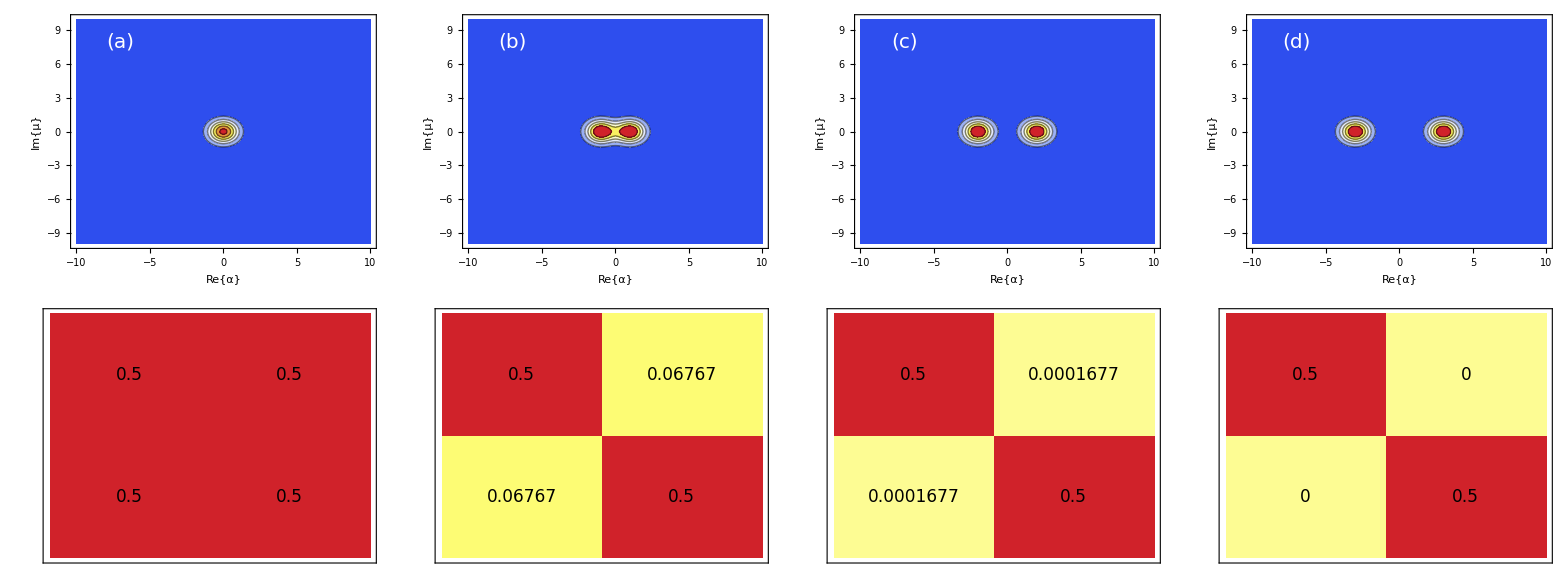

```mathematica
vNmodelExamplePlot1half=Grid[
{
(*First row - Contour plot of the Q-function*)
Table[Quiet@ContourPlot[Quiet@Q1half/. g0t->c/. reμ->x/. imμ->y,{x,-10,10},{y,-10,10},Epilog->Inset[Style[alphabetlabel[[c+1]],White,FontSize->20],{-7,8}],PlotPoints->40,PlotRange->All,ImageSize->400,ColorFunction->"TemperatureMap",FrameStyle->Black,FrameLabel->{Style["Re{α}",Black,FontSize->20],Style["Im{μ}",Black,FontSize->20]},AxesLabel->{{Style["Re{μ}",Black,FontSize->20],None},Style["Im{α}",Black,FontSize->20]},TicksStyle->Directive[Black,FontSize->20]  (*Set ticks style to black and fontsize 20*)],{c,{0,1,2,3}}]
,

(*Second row - Hinton diagram of the density matrix*)
Table[MatrixPlot[ρt1half/.g0t->c,
FrameTicks->None,
ColorFunction->"TemperatureMap",
ImageSize->350,
Epilog->Table[Text[Style[Chop@N[ρt1half[[i,j]]/.g0t->c,4],17],{j-0.5,Length[ρt1half]-i+0.5}],{i,Length[ρt1half]},{j,Length[ρt1half[[i]]]}]
],{c,{0,1,2,5}}]
}

]
Export[PlotsPathChap1<>"vNmodelExample1half.pdf",vNmodelExamplePlot1half];
```

```mathematica
Qplusonehalf=1/π(Exp[-Abs[(reμ + ⅈ imμ) - g0t/2 ]^2])//cf
Qminusonehalf=1/π(Exp[-Abs[(reμ + ⅈ imμ) + g0t/2 ]^2])//cf
```

(ⅇ^(-Abs[-g0t/2+ⅈ imμ+reμ]^2))/π

(ⅇ^(-Abs[g0t/2+ⅈ imμ+reμ]^2))/π

```mathematica
Integrate[Integrate[Qplusonehalf,{reμ,-20,20}],{imμ,-20,20}]
```

1/4 (Erf[20-Im[g0t]/2]+Erf[20+Im[g0t]/2]) (Erf[20-Re[g0t]/2]+Erf[20+Re[g0t]/2])

```mathematica
1/4 (Erf[20-Im[g0t]/2]+Erf[1/2 (40+Im[g0t])]) (Erf[20-Re[g0t]/2]+Erf[20+Re[g0t]/2])//cf
```

1/2 Erf[20] (Erf[20-g0t/2]+Erf[20+g0t/2])

```mathematica
argOfintegral=√(Qplusonehalf Qminusonehalf)//cf
```

(ⅇ^(-g0t^2/4-imμ^2-reμ^2))/π

```mathematica
cBhatToyModel=Integrate[Integrate[argOfintegral,{reμ,-20,20}],{imμ,-20,20}]
```

ⅇ^(-g0t^2/4)

```mathematica
qℬhatToyModel=Abs[Tr[σx.ρt1half]]//cf
```

ⅇ^(-2 g0t^2)

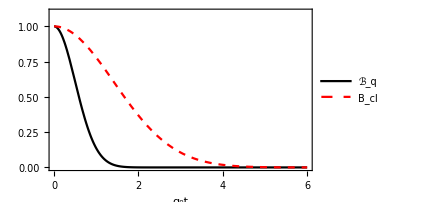

```mathematica
ToyModelcandqBhat=Plot[{qℬhatToyModel, cBhatToyModel},{g0t,0,6},
PlotStyle->{{Black},{Dashed,Red}},
PlotRange->{All,{0,1.1}},
PlotLegends->legend[{"ℬ_q","B_cl"},{0.85,0.8}],
FrameLabel->{"g_0t",None}]
Export[PlotsPathChap1<>"ToyModelcandqBhat1half.pdf",ToyModelcandqBhat];
```

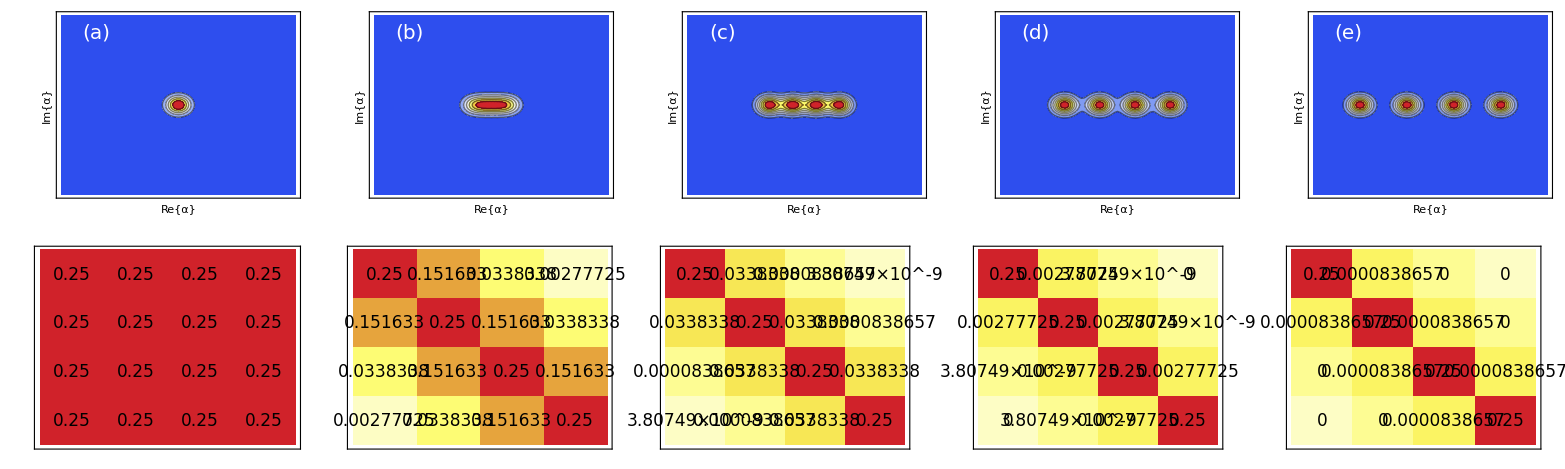

```mathematica
vNmodelExamplePlot3half=Grid[
{
(*First row - Contour plot of the Q-function*)
Table[
Quiet@ContourPlot[Quiet@Q3half/.g0t->c/.reμ->x/.imμ->y,{x,-10,10},{y,-10,10},
Epilog->Inset[Style[alphabetlabel[[c+1]],White,FontSize->20],{-7,8}],
PlotPoints->40,
ImageSize->500,
PlotRange->All,
ColorFunction->"TemperatureMap",
FrameTicks->None,
AxesLabel->{"Re{α}","Im{α}"}],{c,{0,1,2,3,4}}],

(*Second row - Hinton diagram of the density matrix*)
Table[MatrixPlot[ρt3half/.g0t->c,
ColorFunction->"TemperatureMap",
PlotTheme->"Business",
ImageSize->500,
FrameTicks->None,
Epilog->Table[Text[Style[Chop@N[ρt3half[[i,j]]/.g0t->c,4],17],{j-0.5,Length[ρt3half]-i+0.5}],{i,Length[ρt3half]},{j,Length[ρt3half[[i]]]}],
FrameTicks->{{1,MX@" "},{2,MX@" "},{3,MX@" "},{4,MX@" "}}],{c,{0,1,2,3,4}}]

}

]
Export[PlotsPathChap1<>"vNmodelExample3half.pdf",vNmodelExamplePlot3half];
```

Playing with Manipulate:

```mathematica
Manipulate[
ContourPlot[Quiet@Q1half/.g0t->c/.reμ->x/.imμ->y,{x,-10,10},{y,-10,10},PlotPoints->90,PlotRange->All,ColorFunction->"TemperatureMap",AxesLabel->{"Re{α}","Im{α}"},Epilog->Inset[Style["g_0t="<>ToString[c],White],{5,8}]],{c,0,5,0.01}]
```

```mathematica
Manipulate[
ContourPlot[Quiet@Q3half/.g0t->c/.reμ->x/.imμ->y,{x,-10,10},{y,-10,10},PlotPoints->90,PlotRange->All,ColorFunction->"TemperatureMap",AxesLabel->{"Re{α}","Im{α}"},Epilog->Inset[Style["g_0t="<>ToString[c],White],{5,8}]],{c,0,5,0.01}]
```

Making cool gifs:

```mathematica
PrettyTiming[AnimQfunc=Table[Quiet@ContourPlot[Quiet@Q1half/.g0t->c/.reμ->x/.imμ->y,{x,-10,10},{y,-10,10},PlotPoints->40,PlotRange->All,ColorFunction->"TemperatureMap",AxesLabel->{"Re{α}","Im{α}"},Epilog->Inset[Style["g_0t="<>ToString[c],FontSize->30],{5,8}]],{c,0,5,0.1}];
Animρt=Table[
MatrixPlot[ρt1half/.g0t->c,
FrameTicks->None,
ColorFunction->"TemperatureMap",
ImageSize->350,
Epilog->Table[Text[Style[Chop@N[ρt1half[[i,j]]/.g0t->c,4],17],{j-0.5,Length[ρt1half]-i+0.5}],{i,Length[ρt1half]},{j,Length[ρt1half[[i]]]}]
],
{c,0,5,0.1}];]
```

0h : 0m : 9s

```mathematica
Export[PlotsPathChap1<>"GifQfunction1half.gif",AnimQfunc];
Export[PlotsPathChap1<>"GifDensityMatrix1half.gif",Animρt];
```

```mathematica
PrettyTiming[AnimQfunc=Table[Quiet@ContourPlot[Quiet@Q3half/.g0t->c/.reμ->x/.imμ->y,{x,-10,10},{y,-10,10},PlotPoints->40,PlotRange->All,ColorFunction->"TemperatureMap",AxesLabel->{"Re{α}","Im{α}"},Epilog->Inset["g_0t="<>ToString[c],{5,8}]],{c,0,5,0.1}];
Animρt=Table[
MatrixPlot[ρt3half/.g0t->c,
ColorFunction->"TemperatureMap",
PlotTheme->"Business",
ImageSize->500,
FrameTicks->None,
Epilog->Table[Text[Style[Chop@N[ρt3half[[i,j]]/.g0t->c,4],17],{j-0.5,Length[ρt3half]-i+0.5}],{i,Length[ρt3half]},{j,Length[ρt3half[[i]]]}],
FrameTicks->{{1,MX@" "},{2,MX@" "},{3,MX@" "},{4,MX@" "}}],
{c,0,5,0.1}];]
```

0h : 0m : 18s

```mathematica
Export[PlotsPathChap1<>"GifQfunction3half.gif",AnimQfunc];
Export[PlotsPathChap1<>"GifDensityMatrix3half.gif",Animρt];
```